```mathematica
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

## Nishikawa,Tanaka sum rule

### qqbar condensate

```mathematica
A=1/2*(w*λ+λ^2/8);
d=4-2*eps;

test1=Integrate[A^(-2+d/2),{λ,0,Infinity},GenerateConditions->False]
```

(2 w^(1-2 eps) 1-eps eps-1/2)/(√π)

```mathematica
Subscript[C3H, q]=Series[1/4*Subscript[α, S]*4*Pi*Subscript[C, F]*μ^(2*eps)*test1/d*1/(2^d*Pi^(d/2))*Gamma[1+d/2]*Gamma[2-d/2]/(Gamma[d/2]*Gamma[3]),{eps,0,0}]//FullSimplify
```

-(w C_F α_S)/(16 π eps)+(w C_F α_S (-2 log(μ)+2 log(w)+ℽ-2-log(π)))/(16 π)+O(eps^1)

```mathematica
test2=Integrate[A^(-3+d/2)*λ^2,{λ,0,Infinity},GenerateConditions->False]

Series[-μ^(2*eps)*test2*1/16*1/(2^d*Pi^(d/2))*Gamma[3-d/2]/(Gamma[3]),{eps,0,0}]//FullSimplify
```

(2^(7-2 eps) w^(1-2 eps) 2-eps 2 eps-1)/(eps+1)

w/(8 π^2 eps)+(w (2 log(μ)-2 log(w)-ℽ+1+log(π)))/(8 π^2)+O(eps^1)

```mathematica
(1+DiracSlash[v])/2*DiracSlash[v]//DiracSimplify
```

1/2 (γ̄·v̄)^2+(γ̄·v̄)/2

## Diagonal hadronic matrix element

### Master Integral

```mathematica
MI[p_,α_,Δ_,β_]:=μ^(2*ϵ)*I*(-1)^(α+β)/(2^(d)*Pi^(d/2))*Gamma[α+d/2]*Gamma[β-α-d/2]/(Gamma[d/2]*Gamma[β])*Δ^(α-β+d/2)
```

### Two Loop leading term

#### First Loop over l

```mathematica
(l^2)*(1-x)+(k-l-ω*v)^2*x//Expand//Simplify
```

-2 l x (k-v ω)+x (k-v ω)^2+l^2

```mathematica
ClearAll[Amp,Amp1,Amp2];
(*For better understanding especially the shift see notes*)
(*Tensor to scalar*)
TS[μ_,ν_]:=FV[l,μ]*FV[l,ν]->l^2/d*MT[μ,ν];


Amp=-(FV[l,μ]*FV[l,ρ])*MT[ν,σ]+(FV[l,ν]*FV[l,ρ])*MT[μ,σ]+(FV[l,μ]*FV[l,σ])*MT[ν,ρ]-(FV[l,ν]*FV[l,σ])*MT[μ,ρ]//ExpandScalarProduct//DiracSimplify//Expand;



Amp=(FV[k,α]*GA[α]*(1-x)-FV[l,α]*GA[α]+ω*FV[v,α]*GA[α]*(x-1))*Amp//ExpandScalarProduct//DiracSimplify//Expand ;

(*Shift loop variable*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[l]]->(FV[l,μ]+FV[k,μ]*(1-x)-FV[v,μ]*ω*(1-x));

Amp=Amp/.{shift[μ],shift[ν],shift[ρ],shift[σ]}//Expand;
```

```mathematica
Amp11=Coefficient[Amp,FV[l,μ]*FV[l,σ]]*FV[l,μ]*FV[l,σ]/.DiracSlash[l]->0//Simplify;
Amp12=Coefficient[Amp,FV[l,μ]*FV[l,ρ]]*FV[l,μ]*FV[l,ρ]/.DiracSlash[l]->0//Simplify;
Amp13=Coefficient[Amp,FV[l,ν]*FV[l,σ]]*FV[l,ν]*FV[l,σ]/.DiracSlash[l]->0//Simplify;
Amp14=Coefficient[Amp,FV[l,ν]*FV[l,ρ]]*FV[l,ν]*FV[l,ρ]/.DiracSlash[l]->0//Simplify;

Amp1=Amp11+Amp12+Amp13+Amp14/.{FV[l,μ]*FV[l,ρ]->(l^2/d)*MT[μ,ρ],FV[l,μ]*FV[l,σ]->(l^2/d)*MT[μ,σ],FV[l,ν]*FV[l,ρ]->(l^2/d)*MT[ν,ρ],FV[l,ν]*FV[l,σ]->(l^2/d)*MT[ν,σ]}//DiracSimplify//Simplify

Subscript[Δ, 1]=-(k-ω*v)^2*(1-x)*x;
(*/.k->2/.v*ω->1; ist dafür da damit ist aus den zähler verschwindet*)
Loop11=MI[l,1,Subscript[Δ, 1],2]/.k->2/.v*ω->1;
Loop11=Loop11*Amp1/.l^2->1//Simplify
```

(l^2 (x-1) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ) (γ̄·k̄-ω γ̄·v̄))/(eps-2)

-(ⅈ (4 π)^(eps-2) (x-1) ((x-1) x)^(1-eps) 3-eps eps-1 μ^(2 ϵ) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ) (γ̄·k̄-ω γ̄·v̄))/((eps-2) 2-eps)

```mathematica
Amp2=Amp/.FV[l,μ]->0/.FV[l,ν]->0/.FV[l,ρ]->0/.FV[l,σ]->0/.DiracSlash[l]->0;
Subscript[Δ, 1]=-(k-ω*v)^2*(1-x)*x;
Loop12=MI[l,0,Subscript[Δ, 1],2]/.k->2/.v*ω->1;
Loop12=Loop12*Amp2//Expand;
```

#### Second Loop over k

```mathematica
(*Denominator has the expression in the Feynman parametrization*)
(k-ω*v)^2+2*v*k*λ//Expand//Simplify;
```

```mathematica
Subscript[g, S]=Subscript[α, S]*4*Pi;
d=4-2*ϵ;
Vorfaktor=2*Subscript[C, F]*I^4*Subscript[g, S]*Subscript[N, C];
(*shift k -> k-v (lambda -w)*)
Subscript[Amp1, K]=Loop11/.DiracSlash[k]->FV[k,α]*GA[α]/.FV[k,α]->(FV[k,α]-FV[v,α](λ-ω));
(*FV[k,α] is zero in the loop integral;so set it to zero*)
Subscript[Amp1, K]=Subscript[Amp1, K]/.FV[k,α]->0//DiracSimplify//Simplify
Subscript[Δ, 2]=λ^2-2*λ*ω;
Loop21=2*Gamma[ϵ]/(Gamma[ϵ-1])*Subscript[Amp1, K]*MI[k,0,Subscript[Δ, 2],ϵ]//Simplify;
(*=========================*)
Integrate[Vorfaktor*Loop21,{λ,0,Infinity},{x,0,1},GenerateConditions->False]//Simplify;
Loop21=Normal@Series[%,{ϵ,0,0}]
```

(ⅈ (4 π)^(eps-2) λ (x-1) ((x-1) x)^(1-eps) 3-eps eps-1 μ^(2 ϵ) γ̄·v̄ ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ))/((eps-2) 2-eps)

-(2^(2 eps-3) ⅇ^(ⅈ π (1-eps)) π^(eps-3) ω^6 C_F N_C (3-eps)^2 eps-1 α_S γ̄·v̄ ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ))/(15 (eps-2) 5-2 eps)

```mathematica
(*shift k -> k-v (lambda -w)*)
Loop12=Loop12/.DiracSlash[k]->FV[k,α]*GA[α]/.FV[k,α]->(FV[k,α]-FV[v,α](λ-ω))/.FV[k,μ]->(FV[k,μ]-FV[v,μ](λ-ω))/.FV[k,ν]->(FV[k,ν]-FV[v,ν](λ-ω))/.FV[k,ρ]->(FV[k,ρ]-FV[v,ρ](λ-ω))/.FV[k,σ]->(FV[k,σ]-FV[v,σ](λ-ω));
Loop12=Loop12//Expand//Simplify;
(*====================================================*)
Loop12=Loop12/.FV[k,α]->0/.FV[k,μ]*FV[k,ρ]->(k^2/d)*MT[μ,ρ]/.FV[k,μ]*FV[k,σ]->(k^2/d)*MT[μ,σ]/.FV[k,ν]*FV[k,ρ]->(k^2/d)*MT[ν,ρ]/.FV[k,ν]*FV[k,σ]->(k^2/d)*MT[ν,σ];
Loop12=Loop12/.FV[k,α]->0/.FV[k,μ]->0/.FV[k,ν]->0/.FV[k,ρ]->0/.FV[k,σ]->0//Expand;
(*====================================================*)

Subscript[Amp21, K]=Coefficient[ Loop12,k^2]//DiracSimplify//FullSimplify;
Subscript[Amp22, K]=Loop12/.k^2->0//DiracSimplify//FullSimplify;

Subscript[Δ, 2]=λ^2-2*λ*ω;

Loop22=2*Gamma[1+ϵ]/(Gamma[ϵ])*Subscript[Amp21, K]*MI[k,1,Subscript[Δ, 2],1+ϵ]//Simplify;
Loop23=2*Gamma[1+ϵ]/(Gamma[ϵ])*Subscript[Amp22, K]*MI[k,0,Subscript[Δ, 2],1+ϵ]//Simplify;
(*=========================*)
Loop22=Integrate[Vorfaktor*Loop22,{x,0,1},{λ,0,Infinity},GenerateConditions->False]//DiracSimplify//FullSimplify;
Loop22=Normal@Series[Loop22,{ϵ,0,0}]
(*=========================*)
Loop23=Integrate[Vorfaktor*Loop23,{x,0,1},{λ,0,Infinity},GenerateConditions->False]//DiracSimplify//FullSimplify;
Loop23=Normal@Series[Loop23,{ϵ,0,0}]
```

-(2^(2 eps-4) ⅇ^(-ⅈ π eps) π^(eps-2) ω^6 C_F N_C csc(π eps) 4-eps α_S (ḡ)^μρ (ḡ)^νσ γ̄·v̄)/(15 5-2 eps)

(2^(2 eps-1) ⅇ^(-ⅈ π eps) π^(eps-2) ω^6 C_F N_C csc(π eps) 4-eps α_S γ̄·v̄ ((v̄)^ν ((v̄)^σ (ḡ)^μρ-(v̄)^ρ (ḡ)^μσ)+(v̄)^μ ((v̄)^ρ (ḡ)^νσ-(v̄)^σ (ḡ)^νρ)))/(15 5-2 eps)

```mathematica
(*Bug is test1 must vanish since i get 3 g^(mu rho) g^(nu sigma)*)
test1=Coefficient[Loop22,Log[-ω]]*Log[-ω]+Coefficient[Loop22,Log[μ]]*Log[μ];
test2=Coefficient[Loop23,Log[-ω]]*Log[-ω]+Coefficient[Loop23,Log[μ]]*Log[μ];

final=Collect[Loop23+Loop21,{ϵ}]
```

(2^(2 eps-1) ⅇ^(-ⅈ π eps) π^(eps-2) ω^6 C_F N_C csc(π eps) 4-eps α_S γ̄·v̄ ((v̄)^ν ((v̄)^σ (ḡ)^μρ-(v̄)^ρ (ḡ)^μσ)+(v̄)^μ ((v̄)^ρ (ḡ)^νσ-(v̄)^σ (ḡ)^νρ)))/(15 5-2 eps)-(2^(2 eps-3) ⅇ^(ⅈ π (1-eps)) π^(eps-3) ω^6 C_F N_C (3-eps)^2 eps-1 α_S γ̄·v̄ ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ))/(15 (eps-2) 5-2 eps)

```mathematica
(*Marcel results*)
LL=-1/2*(MT[μ,ρ]*MT[ν,σ]-MT[μ,σ]*MT[ν,ρ])*(-1)*Subscript[g, S]/(4*Pi^4)*Subscript[N, C]*ω^6*(-1/180*Log[-ω/μ])-1/2*(-MT[ν,σ]*FV[v,μ]*FV[v,ρ]+MT[μ,σ]*FV[v,ν]*FV[v,ρ]+MT[ν,ρ]*FV[v,μ]*FV[v,σ]-MT[μ,ρ]*FV[v,ν]*FV[v,σ])*Subscript[α, S]/Pi^3*Subscript[C, F]*Subscript[N, C]*ω^6*(-1/90*Log[-ω/μ])*(-1)
```

-(ω^6 C_F N_C α_S log(-ω/μ) (-(v̄)^ν (v̄)^σ (ḡ)^μρ+(v̄)^ν (v̄)^ρ (ḡ)^μσ+(v̄)^μ (v̄)^σ (ḡ)^νρ-(v̄)^μ (v̄)^ρ (ḡ)^νσ))/(180 π^3)-(ω^6 N_C α_S log(-ω/μ) ((ḡ)^μρ (ḡ)^νσ-(ḡ)^μσ (ḡ)^νρ))/(360 π^3)

### Quark-Quark condensate (dimension 3)

```mathematica
ClearAll[Amp,Amp1,Amp2];
(*For better understanding especially the shift see notes*)
(*Tensor to scalar*)
TS[μ_,ν_]:=FV[k,μ]*FV[k,ν]->k^2/d*MT[μ,ν];


Amp=-(FV[k,μ]+FV[v,μ]*ω)*(FV[k,ρ]+FV[v,ρ]*ω)*MT[ν,σ]+(FV[k,ν]+FV[v,ν]*ω)*(FV[k,ρ]+FV[v,ρ]*ω)*MT[μ,σ]+(FV[k,μ]+FV[v,μ]*ω)*(FV[k,σ]+FV[v,σ]*ω)*MT[ν,ρ]-(FV[k,ν]+FV[v,ν]*ω)*(FV[k,σ]+FV[v,σ]*ω)*MT[μ,ρ]//ExpandScalarProduct//DiracSimplify//Expand;

(*Shift loop variable*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[k]]->(FV[k,μ]+FV[v,μ]*(λ-ω));

Amp=Amp/.{shift[μ],shift[ν],shift[ρ],shift[σ]}//Expand;


rule1=Outer[TS,{μ,ν,σ,ρ},{μ,ν,ρ,σ}]//Simplify;


Amp1=Coefficient[Amp,FV[k,μ]*FV[k,ρ]]*FV[k,μ]*FV[k,ρ]+Coefficient[Amp,FV[k,μ]*FV[k,σ]]*FV[k,μ]*FV[k,σ]+Coefficient[Amp,FV[k,ν]*FV[k,ρ]]*FV[k,ν]*FV[k,ρ]+Coefficient[Amp,FV[k,ν]*FV[k,σ]]*FV[k,ν]*FV[k,σ];

Amp1=Amp1/.{TS[μ,ρ],TS[μ,σ],TS[ν,ρ],TS[ν,σ]}//DiracSimplify//Simplify


Amp2=Coefficient[Amp,FV[v,μ]*FV[v,ρ]]*FV[v,μ]*FV[v,ρ]+Coefficient[Amp,FV[v,μ]*FV[v,σ]]*FV[v,μ]*FV[v,σ]+Coefficient[Amp,FV[v,ν]*FV[v,ρ]]*FV[v,ν]*FV[v,ρ]+Coefficient[Amp,FV[v,ν]*FV[v,σ]]*FV[v,ν]*FV[v,σ]/.ω->0//Simplify
```

(k^2 ((ḡ)^μρ (ḡ)^νσ-(ḡ)^μσ (ḡ)^νρ))/(ϵ-2)

λ^2 ((v̄)^ν ((v̄)^ρ (ḡ)^μσ-(v̄)^σ (ḡ)^μρ)+(v̄)^μ ((v̄)^σ (ḡ)^νρ-(v̄)^ρ (ḡ)^νσ))

```mathematica
(*Definition of Subscript[I, 1qqbar] and Subscript[I, 2qqbar] is given in the notes *)
Δ=(-2*ω*λ+λ^2);
d=4-2*ϵ;
(*Think it as gs^2*)
Subscript[g, S]=Subscript[α, S]*4*Pi;
Vorfaktor=Subscript[C, F]*I^3*Subscript[g, S]*2/4;


(*========================================*)
resultAmp1=Integrate[Vorfaktor*MI[k,1,Δ,2]*Coefficient[Amp1,k^2],{λ,0,Infinity},Assumptions->{0<a<1},GenerateConditions->False]//Simplify;

resultAmp1=Normal@Series[resultAmp1,{ϵ,0,0}];
(*========================================*)


(*========================================*)
resultAmp2=Integrate[Vorfaktor*MI[k,0,Δ,2]*Amp2,{λ,0,Infinity},Assumptions->{0<a<1},GenerateConditions->False]//Simplify;

resultAmp2=Normal@Series[resultAmp2,{ϵ,0,0}];
(*========================================*)

QQCondensate=resultAmp1+resultAmp2/.ϵ->Infinity/.Log[Pi]->0/.EulerGamma->0;

QQCondensate=Coefficient[QQCondensate,Log[-ω]]*Log[-ω]+Coefficient[QQCondensate,Log[μ]]*Log[μ];
QQCondensate=QQCondensate/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(ω^3 C_F α_S log(-ω/μ) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ+2 (v̄)^ν ((v̄)^σ (ḡ)^μρ-(v̄)^ρ (ḡ)^μσ)+(v̄)^μ (2 (v̄)^ρ (ḡ)^νσ-2 (v̄)^σ (ḡ)^νρ)))/(6 π)

### Gluon-Gluon condensate (dimension 4)

```mathematica
ClearAll[Amp,Amp1,Amp2];
(*Tensor to scalar*)
TS[μ_,ν_]:=FV[k,μ]*FV[k,ν]->k^2/d*MT[μ,ν];

Amp=(FV[k,α]*GA[α]+FV[v,α]*GA[α]*ω)*(MT[μ,ρ]*MT[ν,σ]-MT[μ,σ]*MT[ν,ρ])//ExpandScalarProduct//Expand;

(*Shift loop variable*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[k]]->(FV[k,μ]+FV[v,μ]*(λ-ω));

Amp=Amp/.shift[α]//Expand;

Amp=Amp/.FV[k,α]->0//DiracSimplify//Simplify
```

λ γ̄·v̄ ((ḡ)^μρ (ḡ)^νσ-(ḡ)^μσ (ḡ)^νρ)

```mathematica
Δ=(-2*ω*λ+λ^2);
d=4-2*ϵ;
(*Think it as gs^2*)
(*Gluon-Gluon matrix element = 1/(d*(d-1))*1/(Nc^2-1)*<G^2>*)
g=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=I^3*g^2*1/(12);

(*========================================*)
resultAmp=Integrate[Vorfaktor*MI[k,0,Δ,2]*Amp,{λ,0,Infinity},GenerateConditions->False]//Simplify;
resultAmp=Normal@Series[4^(-ϵ)*resultAmp,{ϵ,0,0}]//FullSimplify;

resultAmp=Collect[resultAmp,{ϵ}]
(*========================================*)
(*Zieh Faktor -1/2 raus*)
GGCondensate=Coefficient[resultAmp,Log[-ω]]*Log[-ω]+Coefficient[resultAmp,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(ω^2 α_S (-2 log(μ)+2 log(-ω)+ℽ-2-log(π)+log(4)) γ̄·v̄ ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ))/(48 π)-(ω^2 α_S γ̄·v̄ ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ))/(48 π ϵ)

(ω^2 α_S log(-ω/μ) γ̄·v̄ ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ))/(24 π)

```mathematica
(*Marcel result*)
MGG=DiracSlash[v]*(MT[μ,ρ].MT[ν,σ]-MT[μ,σ].MT[ν,ρ])*(-1)*Subscript[α, S]/Pi*ω^2*(-1/12)*Log[ω/μ]
```

(ω^2 α_S log(ω/μ) γ̄·v̄ ((ḡ)^μρ.(ḡ)^νσ-(ḡ)^μσ.(ḡ)^νρ))/(12 π)

```mathematica
Subscript[Γ, 1]=I*FV[v,ν].FV[v,α].Sigma[μ,α].GA5;
Subscript[Γ, 2]=I*FV[v,σ].FV[v,α].Sigma[ρ,α].GA5;
P=(1+DiracSlash[v])/2;
LorentzStructure=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]//Contract;
LorentzStructure/.Pair[Momentum[v],Momentum[v]] ->1//Simplify
```

-(ω^2 α_S log(-ω/μ) Sigma(μ,α) Sigma(ρ,α) ((ḡ)^μρ-(v̄)^μ (v̄)^ρ))/(12 π)

#### Quark-Gluon condensate (dimension 5)

##### 1 Contribution -Graphics-

```mathematica
amp =( (-ω*FV[v,σ]+FV[k,σ]).MT[ρ,λ]- (-ω*FV[v,ρ]+FV[k,ρ]).MT[σ,λ]).GA[λ];
amp=(-ω*FV[v,x].GA[x]+FV[k,x].GA[x]).amp//ExpandScalarProduct//DiracSimplify//Expand;
(*shift variable k*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[k]]->(FV[k,μ]-FV[v,μ]*(Subscript[λ, 1]-ω));
(*Die ω müssen verschwinden im Zähler aber Feyncalc macht das aus irgendeinen grund nicht.*)
amp = amp/.{shift[x],shift[σ],shift[ρ]}/.ω->0//ExpandScalarProduct//DiracSimplify//Expand

amp= -k^2/d*MT[ρ,α].GA[α].GA[σ]+k^2/d*MT[σ,α].GA[α].GA[ρ]+Subscript[λ, 1]*ω*(FV[v,ρ].DiracSlash[v].GA[σ]-FV[v,σ].DiracSlash[v].GA[ρ]);
```

(k̄)^ρ (-(γ̄·k̄).(γ̄)^σ)+(k̄)^σ (γ̄·k̄).(γ̄)^ρ+λ_1 (v̄)^ρ (γ̄·k̄).(γ̄)^σ-λ_1 (v̄)^σ (γ̄·k̄).(γ̄)^ρ

```mathematica
Subscript[Δ, 1]=-2*Subscript[λ, 1]*ω+Subscript[λ, 1]^2;
d=4-2*ϵ;
gs=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=4*I^4*gs^2/48*qGC*Subscript[C, F];
qGCondensate = MI[k,1,Subscript[Δ, 1],3]*Coefficient[amp,k^2];

qGCondensate =Integrate[Vorfaktor*qGCondensate,{Subscript[λ, 1],0,Infinity},GenerateConditions->False]//Simplify;

qGCondensate=Normal@Series[qGCondensate,{ϵ,0,0}]//Contract//ExpandScalarProduct//DiracSimplify//FullSimplify;

qGCondensate=Collect[qGCondensate,{ϵ}]

qGCondensate =( Coefficient[qGCondensate,Log[-ω]]*Log[-ω]+ Coefficient[qGCondensate,Log[μ]]*Log[μ])/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(ⅈ qGC ω C_F α_S (-2 log(μ)+2 log(-ω)+ℽ-2-log(π)) ((γ̄)^ρ.(γ̄)^σ-(γ̄)^σ.(γ̄)^ρ))/(192 π)-(ⅈ qGC ω C_F α_S ((γ̄)^ρ.(γ̄)^σ-(γ̄)^σ.(γ̄)^ρ))/(192 π ϵ)

(ⅈ qGC ω C_F α_S log(-ω/μ) ((γ̄)^ρ.(γ̄)^σ-(γ̄)^σ.(γ̄)^ρ))/(96 π)

##### 2 Contribution -Graphics-

### QCD Sum Rule

#### Reproducing Tanakas result (Just for fun)

```mathematica
(*Reproducing Eq. (27)*)
Subscript[C, FormLL]=Subscript[N, C]/(2*Pi^2)*ω^2*HeavisideTheta[ω];
Subscript[C, Form3]=-1/2*DiracDelta[ω]*qqC;
Subscript[C, Form5]=1/16*1/2*DiracDelta''[ω]*qGC;

Formfactor=Integrate[2*Exp[-ω/M]*(Subscript[C, FormLL]+Subscript[C, Form3]+Subscript[C, Form5]),{ω,0,Subscript[ω, th]},Assumptions->0<Subscript[ω, th]<1,GenerateConditions->False]/.HeavisideTheta[0]->1/.HeavisideTheta[0,Subscript[ω, th]]->1//Simplify
```

(N_C (2 M^3-M ⅇ^(-ω_th/M) (2 M^2+2 M ω_th+ω_th^2)))/π^2+qGC/(16 M^2)-qqC

-(ω_th^2 ⅇ^(-ω_th/M))/(2 M^2)-(ω_th ⅇ^(-ω_th/M))/M-ⅇ^(-ω_th/M)+1

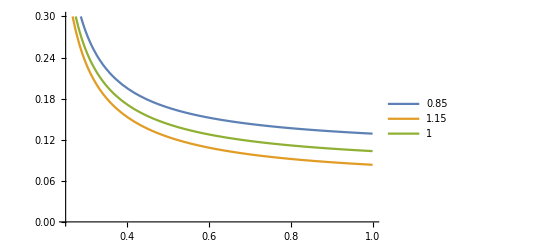

```mathematica
(*Reproducing Figure 3*)
GeV=10^9;
InputParameter={Subscript[N, C]->3,Subscript[α, S]->0.47,Subscript[C, F]->4/3,qqC->(-0.24)^3*GeV^3,ggC->0.012*GeV^4,qGC->0.8*(-0.24)^3*GeV^5};

W[m_,x_]:=1-Sum[(x)^k/k! *Exp[-x],{k,0,m}]

W[2,Subscript[ω, th]/M]

LambdaH=-2*Subscript[α, S]/Pi^3*Subscript[N, C]*Subscript[C, F]*M^5*W[4,Subscript[ω, th]/M]-3*Subscript[α, S]/Pi*Subscript[C, F]*M^2*qqC*W[1,Subscript[ω, th]/M]+M/4*ggC*W[0,Subscript[ω, th]/M]-1/4*qGC;

Plot[{(LambdaH/Formfactor)*10^(-18)/.InputParameter/.Subscript[ω, th]->0.85*GeV,(LambdaH/Formfactor)*10^(-18)/.InputParameter/.Subscript[ω, th]->1.15*GeV,(LambdaH/Formfactor)*10^(-18)/.InputParameter/.Subscript[ω, th]->GeV},{M,0.25*GeV,GeV},PlotLegends->{0.85,1.15,1},PlotRange->{0,0.30}]
```

#### λ_E^2

##### Timelike region ω > 0

```mathematica
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])
Subscript[Γ, 1]=FV[v,ν].FV[v,α].Sigma[μ,α].GA5;
Subscript[Γ, 2]=FV[v,σ].FV[v,α].Sigma[ρ,α].GA5;
P=(1+DiracSlash[v])/2;


C1=Subscript[λ, H]^2*TR[Subscript[Γ, 1].P.GA5.Sigma[μ,ν]]+(Subscript[λ, H]^2-Subscript[λ, E]^2)*TR[Subscript[Γ, 1].P.GA5.vTensor[μ,ν]]/.Pair[Momentum[v],Momentum[v]] ->1//Simplify
C2=Subscript[λ, H]^2*TR[GA5.P.Subscript[Γ, 2].Sigma[ρ,σ]]-(Subscript[λ, H]^2-Subscript[λ, E]^2)*TR[GA5.P.Subscript[Γ, 2].vTensor[ρ,σ]]/.Pair[Momentum[v],Momentum[v]] ->1//Simplify

(-I)^2/36*C1*C2
```

6 λ_ⅇ^2

6 λ_ⅇ^2

-λ_ⅇ^4

##### Spacelike region ω < 0

```mathematica
GeV=10^9;
InputParameter={Subscript[N, C]->3,Subscript[α, S]->0.47,Subscript[C, F]->4/3,qqC->(-0.24)^3*GeV^3,ggC->0.012*GeV^4,qGC->0.8*(-0.24)^3*GeV^5};
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])
Subscript[Γ, 1]=I*FV[v,ν].FV[v,α].Sigma[μ,α].GA5;
Subscript[Γ, 2]=I*FV[v,σ].FV[v,α].Sigma[ρ,α].GA5;
P=(1+DiracSlash[v])/2;
qGCondensate=qGC*ω*Subscript[α, S]/(24*Pi)*(-HeavisideTheta[ω]);
(*Der Faktor Pi/Subscript[α, S]in ggC kommt wegen der definition von Gluon Kondensat <Subscript[α, S]/Pi*G^2>*)
sumrule1=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].Sigma[μ,ν].Sigma[ρ,σ]]*qGCondensate//Contract;



sumrule1=sumrule1/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;


sumrule1=Integrate[sumrule1*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<GeV,0<M<GeV},GenerateConditions->False]//Simplify;
```

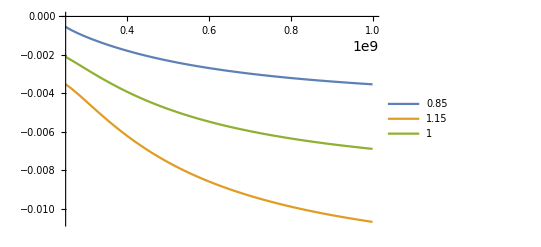

```mathematica
Plot[{(sumrule1/Formfactor)*10^(-36)/.InputParameter/.Subscript[ω, th]->0.85*GeV,(sumrule1/Formfactor)*10^(-36)/.InputParameter/.Subscript[ω, th]->1.15*GeV,(sumrule1/Formfactor)*10^(-36)/.InputParameter/.Subscript[ω, th]->1.0*GeV},{M,0.25*GeV,GeV},PlotLegends->{0.85,1.15,1}]
```

#### λ_H^2

##### Timelike region ω >0

```mathematica
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])
Subscript[Γ, 1]=I*(1/2*Sigma[μ,ν]-FV[v,ν].FV[v,α].Sigma[μ,α]).GA5;
Subscript[Γ, 2]=I*(1/2*Sigma[ρ,σ]-FV[v,σ].FV[v,α].Sigma[ρ,α]).GA5;
P=(1+DiracSlash[v])/2;
(*C1 = -Subscript[λ, H]*TR[Sigma[μ,ν].Subscript[Γ, 1].P.Subscript[Γ, 2].Sigma[ρ,σ]]
C2=Subscript[λ, H]*(Subscript[λ, H]-Subscript[λ, E])*TR[Sigma[μ,ν].Subscript[Γ, 1].P.Subscript[Γ, 2].vTensor[ρ,σ]]
C3=-Subscript[λ, H]*(Subscript[λ, H]-Subscript[λ, E])*TR[vTensor[μ,ν].Subscript[Γ, 1].P.Subscript[Γ, 2].Sigma[ρ,σ]]
C4=(Subscript[λ, H]-Subscript[λ, E])*TR[vTensor[μ,ν].Subscript[Γ, 1].P.Subscript[Γ, 2].vTensor[ρ,σ]]
*)

C1=Subscript[λ, H]*TR[Subscript[Γ, 1].P.GA5.Sigma[μ,ν]]+(Subscript[λ, H]-Subscript[λ, E])*TR[Subscript[Γ, 1].P.GA5.vTensor[μ,ν]]/.Pair[Momentum[v],Momentum[v]] ->1//Simplify;
C2=Subscript[λ, H]*TR[GA5.P.Subscript[Γ, 2].Sigma[ρ,σ]]-(Subscript[λ, H]-Subscript[λ, E])*TR[GA5.P.Subscript[Γ, 2].vTensor[ρ,σ]]/.Pair[Momentum[v],Momentum[v]] ->1//Simplify;

(-I)^2/36*C1*C2//Simplify
```

λ_H^2

##### Spacelike region ω <0

```mathematica
(*TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]*)
```

```mathematica
GeV=10^9;
InputParameter={Subscript[N, C]->3,Subscript[α, S]->0.47,Subscript[C, F]->4/3,qqC->(-0.24)^3*GeV^3,ggC->0.012*GeV^4,qGC->0.8*(-0.24)^3*GeV^5};
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])
Subscript[Γ, 1]=I*(1/2*Sigma[μ,ν]-FV[v,ν].FV[v,α].Sigma[μ,α]).GA5;
Subscript[Γ, 2]=I*(1/2*Sigma[ρ,σ]-FV[v,σ].FV[v,α].Sigma[ρ,α]).GA5;
P=(1+DiracSlash[v])/2;
qGCondensate1=qGC*ω*Subscript[α, S]/(24*Pi)*(-HeavisideTheta[ω]);
(*Der Faktor Pi/Subscript[α, S]in ggC kommt wegen der definition von Gluon Kondensat <Subscript[α, S]/Pi*G^2>*)
sumrule2=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].Sigma[μ,ν].Sigma[ρ,σ]]*qGCondensate//Contract;



sumrule2=sumrule2/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify

sumrule2=Integrate[sumrule2*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<GeV,0<M<GeV},GenerateConditions->False]//Simplify
```

(ω ω (α_S (-60 π^2 qqC ω^2 C_F+ω^5 N_C-15 π^2 qGC)+15 π^3 ggC ω))/(60 π^3)

1/(60 π^3)M ⅇ^(-ω_th/M) (15 π^3 ggC (2 M^2 (ⅇ^(ω_th/M)-1)-2 M ω_th-ω_th^2)-α_S (60 π^2 qqC C_F (6 M^3 (ⅇ^(ω_th/M)-1)-6 M^2 ω_th-3 M ω_th^2-ω_th^3)+N_C (-720 M^6 (ⅇ^(ω_th/M)-1)+720 M^5 ω_th+360 M^4 ω_th^2+120 M^3 ω_th^3+30 M^2 ω_th^4+6 M ω_th^5+ω_th^6)+15 π^2 qGC (M (ⅇ^(ω_th/M)-1)-ω_th)))

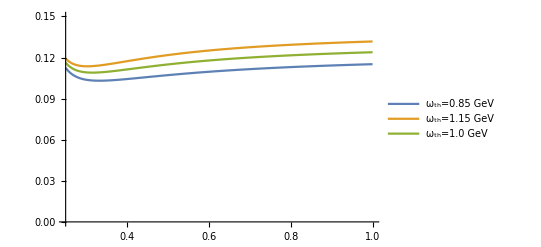

```mathematica
Plot[{Sqrt[(sumrule2/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->0.85GeV,
Sqrt[(sumrule2/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.15GeV,Sqrt[(sumrule2/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.0GeV},{M,0.25*GeV,GeV},PlotLegends->{"ω_th=0.85 GeV","ω_th=1.15 GeV","ω_th=1.0 GeV"},PlotRange->{0,0.15}]
```

```mathematica
Exp[b*t]/(2*(b+a))+Exp[-b*t]/(2*(b-a))//Expand//Simplify
```

1/2 ⅇ^(-b t) (ⅇ^(2 b t)/(a+b)+1/(b-a))